This compares MIDs simulated with OpenFLUX to our MID simulation, to ensure the models behave the same way

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
```

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport

## Get model from DB

### Metabolic network

```mathematica
net=NetworkFromDB["liver-model-2"]
```

<MetabolicNetwork, 89 reactions>

### Atom map

```mathematica
atomMap=AtomMapsFromDB[net,{"C"}];
```

```mathematica
atomMap=RemoveUnreachable[net,atomMap];
Length[atomMap]
```

89

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMap]/.{{ri_Integer,s_List,p_List}:>{Reactions[net]⟦ri⟧,Union[Metabolite/@First/@s],Union[Metabolite/@First/@p]}}
```

{}

```mathematica
CheckAtomMap[atomMap]
```

{}

#### Boundary map

```mathematica
bmap=BoundaryAtomMaps[net,atomMap];
bmap//Length
```

35

### Symmetry

```mathematica
symmetry=GetSymmetryMap[atomMap]
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

### Flux vector from OpenFLUX

```mathematica
fluxState=Block[{ofReactions,ofFluxes,reactionIds,bnet,nu,nr},
{ofReactions,ofFluxes}=Transpose[Import["FluxResults_liver-model-2_openflux_221005.txt","TSV"]];
reactionIds= ReactionID/@Reactions[net];
bnet=BoundaryNetwork[net];
nu=Length[InputMetabolites[net]];
nr=Length[OutputMetabolites[net]];
FluxState@@Replace[
{reactionIds,
Table[StringJoin[r,"_R"],{r,reactionIds}],
Take[BoundaryFluxNames[bnet], nu],
Take[BoundaryFluxNames[bnet], -nr]} ,Append[Thread[Rule[ofReactions,ofFluxes]],_String->0],{2}]]
```

<FluxState, 89 reactions, 35 b. exch>

```mathematica
TableForm[Transpose[{ForwardFlux[fluxState],ReverseFlux[fluxState]}],
TableHeadings->{ ReactionID/@Reactions[net],{"fwd","rev"}}]
```

| fwd | rev
2AMACHYD | 3.77847 | 0
ACITL | 4.957 | 0
ACOAHi | 1.39176 | 0
ACONTm | 202.252 | 199
ACRNtm | 7.35108 | 0
ACS | 3.78583 | 0
ADK1 | 6.21623 | 0
AKGDm | 200.262 | 199
AKGtm | 194.984 | 199
ALATA_L | 8.67103 | 0
ARGN | 2.4304 | 0
ARGSL | 2.4304 | 0
ARGSS | 2.4304 | 0
ASPTA | 90.6357 | 89.7121
ASPTAm | 100.186 | 92.3344
ASPtm | 7.85164 | 0
ATPS4m | 47.1832 | 0
ATPtm | 237.164 | 199
CBPSam | 2.4304 | 0
CELLWORK | 1.46082 | 0
CITtm | 4.957 | 0
CO2tm | 201.479 | 199
CRNtim | 7.35108 | 0
CSm | 8.20904 | 0
CSNATm | 7.35108 | 0
CSNATr | 7.35108 | 0
CYOOm | 10.6803 | 0
CYOR-u10m | 21.3605 | 0
ENO | 195.57 | 199
FBA | 199.596 | 199
FBP | 2.86485 | 0
FUMm | 8.64845 | 0
FUMtm | 2.4304 | 0
G3PD1 | 199.956 | 199
G6PPer | 11.2573 | 0
G6Pter | 11.2573 | 0
GAPD | 20.5981 | 18.4496
GHMT2r | 179.899 | 179.899
GLCter | 11.2573 | 0
GLNtm | 6.27881 | 0
GLUDxm | 72.8928 | 78.7185
GLUNm | 205.279 | 199
GLUt2m | 13.9632 | 18.216
GLYCOGEN_BREAK | 1.49338 | 0
GLYK | 0.95591 | 0
GTHS | 3.25484 | 0
H2Oter | 11.2573 | 0
H2Otm | 160.574 | 199
HCO3Em | 12.807 | 0
HEX1 | 10.3602 | 0
Htm2 | 180.172 | 199
ICDHxm | 23.5925 | 20.3405
LDH_L | 205.63 | 199
MALtm | 1.99165 | 0
MDH | 1.99165 | 0
MDHm | 209.64 | 199
MMEm | 4.95599 | 0
MMMm | 4.95599 | 0
MMSAD1m | 4.95599 | 0
NADH2-u10m | 15.1425 | 0
NADH_REDOX | 0.061676 | 0
NDPK1 | 3.8889 | 0
NH4tm | 17.7797 | 15.8024
O2tm | 10.6803 | 0
OCBTm | 2.4304 | 0
ORNt4m | 2.4304 | 0
PCm | 5.42058 | 0
PDHm | 0.857961 | 0
PEPCK | 3.8889 | 0
PFK | 3.46118 | 0
PGCD | 5.57864 | 0
PGI | 30.3789 | 29.7825
PGK | 201.149 | 199
PGM | 195.57 | 199
PGMT | 1.49338 | 0
PIt2m | 38.1639 | 0
PIter | 11.2573 | 0
PPA | 6.21623 | 0
PPCOACm | 4.95599 | 0
PROTDEG_ALA | 4.07416 | 0
PROTDEG_ARG | 4.06017 | 0
PSERT | 5.57864 | 0
PSP_L | 5.57864 | 0
PYK | 0.458833 | 0
PYRt2m | 34.398 | 28.1195
SERHL | 3.77847 | 0
SUCD1m | 6.21805 | 0
SUCOASm | 6.21805 | 0
TPI | 8.23412 | 6.68187

```mathematica
TableForm[BoundaryFlux[fluxState],TableHeadings->{BoundaryFluxNames[BoundaryNetwork[net]],None}]
```

2mop_IN | 4.95599
ac_IN | 2.39407
ala-L_IN | 4.59687
arg-L_IN | 5.39406
asp-L_IN | 3.88468
co2_IN | 3.62429
energy_IN | 5.59774
glc-D_IN | 1.27611
gln-L_IN | 6.27881
glucys_IN | 3.25484
gly_IN | 3.25484
glyc_IN | 0.95591
glycogen_IN | 1.49338
h2o_IN | 5.90229
h_IN | 0.237011
nh4_IN | 3.54594
o2_IN | 10.6803
pi_IN | 13.9768
prot_ala_IN | 4.07416
prot_arg_IN | 4.06017
ser-L_IN | 0
arg-L_OUT | 9.45423
asp-L_OUT | 8.38238
co2_OUT | 5.03426
energy_OUT | 7.05856
glc-D_OUT | 2.17317
glu-L_OUT | 8.26879
gthrd_OUT | 3.25484
h2o_OUT | 9.69843
h_OUT | 10.6054
lac-L_OUT | 6.6298
nh4_OUT | 5.34714
pi_OUT | 13.9768
ser-L_OUT | 1.80016
urea_OUT | 2.4304

```mathematica
TableForm[Chop[MassBalance[net,fluxState],10^-6],TableHeadings->{Metabolites[net],None}]
```

Metabolite[13dpg,Cytosol,Internal] | 0
Metabolite[2amac,Cytosol,Internal] | 0
Metabolite[2mop,Mitochondria,Uptake] | -4.95599
Metabolite[2pg,Cytosol,Internal] | 0
Metabolite[3pg,Cytosol,Internal] | 0
Metabolite[3php,Cytosol,Internal] | 0
Metabolite[ac,Cytosol,Uptake] | -2.39407
Metabolite[accoa,Cytosol,Internal] | 0
Metabolite[accoa,Mitochondria,Internal] | 0
Metabolite[acrn,Cytosol,Internal] | 0
Metabolite[acrn,Mitochondria,Internal] | 0
Metabolite[adp,Cytosol,Internal] | 0
Metabolite[adp,Mitochondria,Internal] | 0
Metabolite[akg,Cytosol,Internal] | 0
Metabolite[akg,Mitochondria,Internal] | 0
Metabolite[ala-L,Cytosol,Uptake] | -4.59687
Metabolite[amp,Cytosol,Internal] | 0
Metabolite[arg-L,Cytosol,Free] | 4.06017
Metabolite[argsuc,Cytosol,Internal] | 0
Metabolite[asp-L,Cytosol,Free] | 4.4977
Metabolite[asp-L,Mitochondria,Internal] | 0
Metabolite[atp,Cytosol,Internal] | 0
Metabolite[atp,Mitochondria,Internal] | 0
Metabolite[cbp,Mitochondria,Internal] | 0
Metabolite[cit,Cytosol,Internal] | 0
Metabolite[cit,Mitochondria,Internal] | 0
Metabolite[citr-L,Cytosol,Internal] | 0
Metabolite[citr-L,Mitochondria,Internal] | 0
Metabolite[co2,Cytosol,Free] | 1.40997
Metabolite[co2,Mitochondria,Internal] | 0
Metabolite[coa,Cytosol,Internal] | 0
Metabolite[coa,Mitochondria,Internal] | 0
Metabolite[crn,Cytosol,Internal] | 0
Metabolite[crn,Mitochondria,Internal] | 0
Metabolite[dhap,Cytosol,Internal] | 0
Metabolite[energy,Cytosol,Free] | 1.46082
Metabolite[f6p,Cytosol,Internal] | 0
Metabolite[fdp,Cytosol,Internal] | 0
Metabolite[ficytC,Mitochondria,Internal] | 0
Metabolite[focytC,Mitochondria,Internal] | 0
Metabolite[fum,Cytosol,Internal] | 0
Metabolite[fum,Mitochondria,Internal] | 0
Metabolite[g1p,Cytosol,Internal] | 0
Metabolite[g3p,Cytosol,Internal] | 0
Metabolite[g6p,Cytosol,Internal] | 0
Metabolite[g6p,EndoplasmicReticulum,Internal] | 0
Metabolite[gdp,Cytosol,Internal] | 0
Metabolite[glc-D,Cytosol,Free] | 0.897052
Metabolite[glc-D,EndoplasmicReticulum,Internal] | 0
Metabolite[gln-L,Cytosol,Uptake] | -6.27881
Metabolite[gln-L,Mitochondria,Internal] | 0
Metabolite[glucys,Cytosol,Uptake] | -3.25484
Metabolite[glu-L,Cytosol,Release] | 8.26879
Metabolite[glu-L,Mitochondria,Internal] | 0
Metabolite[gly,Cytosol,Uptake] | -3.25484
Metabolite[glyc3p,Cytosol,Internal] | 0
Metabolite[glyc,Cytosol,Uptake] | -0.95591
Metabolite[glycogen,Cytosol,Uptake] | -1.49338
Metabolite[gthrd,Cytosol,Release] | 3.25484
Metabolite[gtp,Cytosol,Internal] | 0
Metabolite[h2o,Cytosol,Free] | 3.79615
Metabolite[h2o,Mitochondria,Internal] | 0
Metabolite[h2o,EndoplasmicReticulum,Internal] | 0
Metabolite[h,Cytosol,Free] | 10.3684
Metabolite[hco3,Mitochondria,Internal] | 0
Metabolite[h_ims,Mitochondria,Internal] | 0
Metabolite[h,Mitochondria,Internal] | 0
Metabolite[icit,Mitochondria,Internal] | 0
Metabolite[lac-L,Cytosol,Release] | 6.6298
Metabolite[mal-L,Cytosol,Internal] | 0
Metabolite[mal-L,Mitochondria,Internal] | 0
Metabolite[mlthf,Cytosol,Internal] | 0
Metabolite[mmcoa-R,Mitochondria,Internal] | 0
Metabolite[mmcoa-S,Mitochondria,Internal] | 0
Metabolite[nad,Cytosol,Internal] | 0
Metabolite[nadh,Cytosol,Internal] | 0
Metabolite[nadh,Mitochondria,Internal] | 0
Metabolite[nad,Mitochondria,Internal] | 0
Metabolite[nh4,Cytosol,Free] | 1.8012
Metabolite[nh4,Mitochondria,Internal] | 0
Metabolite[o2,Cytosol,Uptake] | -10.6803
Metabolite[o2,Mitochondria,Internal] | 0
Metabolite[oaa,Cytosol,Internal] | 0
Metabolite[oaa,Mitochondria,Internal] | 0
Metabolite[orn,Cytosol,Internal] | 0
Metabolite[orn,Mitochondria,Internal] | 0
Metabolite[pep,Cytosol,Internal] | 0
Metabolite[pi,Cytosol,Free] | 0
Metabolite[pi,Mitochondria,Internal] | 0
Metabolite[pi,EndoplasmicReticulum,Internal] | 0
Metabolite[ppcoa,Mitochondria,Internal] | 0
Metabolite[ppi,Cytosol,Internal] | 0
Metabolite[prot_ala,Cytosol,Uptake] | -4.07416
Metabolite[prot_arg,Cytosol,Uptake] | -4.06017
Metabolite[pser-L,Cytosol,Internal] | 0
Metabolite[pyr,Cytosol,Internal] | 0
Metabolite[pyr,Mitochondria,Internal] | 0
Metabolite[q10h2,Mitochondria,Internal] | 0
Metabolite[q10,Mitochondria,Internal] | 0
Metabolite[ser-L,Cytosol,Free] | 1.80016
Metabolite[succ,Mitochondria,Internal] | 0
Metabolite[succoa,Mitochondria,Internal] | 0
Metabolite[thf,Cytosol,Internal] | 0
Metabolite[urea,Cytosol,Release] | 2.4304

Import as EMU flux vector

```mathematica
(*emuFluxVector=Block[{ofReactions,ofFluxes,emuFluxNames},
{ofReactions,ofFluxes}=Transpose[Import["FluxResults_liver-model-2_openflux_221005.txt","TSV"]];
emuFluxNames= EMUFluxMap[net,"reactions"];
Replace[
StringReplace[emuFluxNames,{"_f"->"","_r"->"_R"}],
Thread[Rule[ofReactions,ofFluxes]],{1}]]*)
```

### OpenFLUX Simulated MIDs and targets

TODO: this should be part of an openflux import function

<FluxState, 89 reactions, 35 b. exch>

```mathematica
openFluxMIDs=Import["MIDResults_liver-model-2_openflux_221005.txt","TSV"];
```

```mathematica
targets=Cases[MetaboliteEMUs[atomMap],EMU[Metabolite[Alternatives@@Union[First/@openFluxMIDs],__],__]]
```

{<acrn_c{(17)}>,<acrn_m{(17)}>,<ala-L_c{(123)}>,<arg-L_c{(123456)}>,<asp-L_c{(1234)}>,<asp-L_m{(1234)}>,<citr-L_c{(123456)}>,<citr-L_m{(123456)}>,<g3p_c{(123)}>,<glc-D_c{(123456)}>,<glc-D_r{(123456)}>,<gln-L_c{(12345)}>,<gln-L_m{(12345)}>,<glu-L_c{(12345)}>,<glu-L_m{(12345)}>,<gly_c{(12)}>,<glyc3p_c{(123)}>,<mal-L_c{(1234)}>,<mal-L_m{(1234)}>,<orn_c{(12345)}>,<orn_m{(12345)}>,<ser-L_c{(123)}>}

## EMU model

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMap,bmap,{"C"},targets,symmetry];
Length[emuReactions]
```

964

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

Reactions producing a given metabolite

```mathematica
Sort[Cases[emuReactions,
EMUReaction[ri_Integer,s_EMU,p:EMU[Metabolite["arg-L",__],_],c_]:>EMUReaction[emuReactionNames⟦ri⟧,s,p,c]]]//TableForm
```

EMUReaction[arg-L_IN,<arg-L_i{(12345)}>,<arg-L_c{(12345)}>,1]
EMUReaction[arg-L_IN,<arg-L_i{(123456)}>,<arg-L_c{(123456)}>,1]
EMUReaction[ARGSL_f,<argsuc_c{(12358)}>,<arg-L_c{(12345)}>,1]
EMUReaction[ARGSL_f,<argsuc_c{(12358a)}>,<arg-L_c{(123456)}>,1]
EMUReaction[PROTDEG_ARG_f,<prot_arg_c{(12345)}>,<arg-L_c{(12345)}>,1]
EMUReaction[PROTDEG_ARG_f,<prot_arg_c{(123456)}>,<arg-L_c{(123456)}>,1]

```mathematica
Position[emuReactionNames,"OCBTm_f"]
```

{{86}}

```mathematica
Cases[emuReactions,EMUReaction[80,__]]//TableForm
```

EMUReaction[80,<2mop_m{(4)}>,<co2_m{(1)}>,1]
EMUReaction[80,<2mop_m{(123)}>,<ppcoa_m{(14f)}>,1]
EMUReaction[80,<2mop_m{(2)}>,<ppcoa_m{(f)}>,1]
EMUReaction[80,<2mop_m{(13)}>,<ppcoa_m{(14)}>,1]
EMUReaction[80,<2mop_m{(1)}>,<ppcoa_m{(1)}>,1]
EMUReaction[80,<2mop_m{(3)}>,<ppcoa_m{(4)}>,1]
EMUReaction[80,<2mop_m{(12)}>,<ppcoa_m{(1f)}>,1]

Reactions with non-unity coefficients (due to equivalence classes)

```mathematica
Sort[Cases[emuReactions,
EMUReaction[ri_Integer,s_EMU,p_EMU,c:Except[1]]:>EMUReaction[emuReactionNames⟦ri⟧,s,p,c]]]//TableForm
```

EMUReaction[ARGSL_f,<argsuc_c{(4)}>,<fum_c{(1)|(2)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(6)}>,<fum_c{(1)|(2)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(7)}>,<fum_c{(3)|(4)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(9)}>,<fum_c{(3)|(4)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(47)}>,<fum_c{(13)|(24)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(69)}>,<fum_c{(13)|(24)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(467)}>,<fum_c{(123)|(124)}>,1/2]
EMUReaction[ARGSL_f,<argsuc_c{(469)}>,<fum_c{(123)|(124)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(3)}>,<succ_m{(1)|(2)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(4)}>,<succ_m{(1)|(2)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(f)}>,<succ_m{(3)|(4)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(g)}>,<succ_m{(3)|(4)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(3f)}>,<succ_m{(13)|(24)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(4g)}>,<succ_m{(13)|(24)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(34f)}>,<succ_m{(123)|(124)}>,1/2]
EMUReaction[SUCOASm_f,<succoa_m{(34g)}>,<succ_m{(123)|(124)}>,1/2]

```mathematica
Union[Dimensions/@emuReactions]
```

{{1},{2},{3},{4},{5},{6}}

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[111,<icit_m{(5)}>,<cit_m{(5)}>,1],EMUReaction[3,<ala-L_i{(3)}>,<ala-L_c{(3)}>,1],EMUReaction[90,<oaa_c{(24)}>,<pep_c{(23)}>,1],EMUReaction[124,<glu-L_m{(12345)}>,<gln-L_m{(12345)}>,1],EMUReaction[125,<glu-L_m{(13)}>,<glu-L_c{(13)}>,1],EMUReaction[115,<akg_m{(5)}>,<glu-L_m{(5)}>,1],EMUReaction[115,<asp-L_m{(12)}>,<oaa_m{(12)}>,1],EMUReaction[37,<asp-L_m{(1)}>,<asp-L_c{(1)}>,1],EMUReaction[71,<glc-D_c{(12)}>,<g6p_c{(12)}>,1],EMUReaction[111,<icit_m{(246)}>,<cit_m{(136)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

497

Size of EMU equivalence classes

```mathematica
Tally[Length/@AtomNumbers/@emus]
```

{{1,485},{2,12}}

```mathematica
Complement[targets,emus]
```

{}

Total number of variables (MI fractions)

```mathematica
Total[Map[(Times@@#&),(Dimensions/@emus)+1]]
```

1497

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 217 internals, 42 substrates, 0 condensations >
2 | <EMUEquation (2), 150 internals, 27 substrates, 6 condensations >
3 | <EMUEquation (3), 78 internals, 13 substrates, 5 condensations >
4 | <EMUEquation (4), 24 internals, 2 substrates, 4 condensations >
5 | <EMUEquation (5), 15 internals, 3 substrates, 2 condensations >
6 | <EMUEquation (6), 13 internals, 4 substrates, 2 condensations >

### Specify input isotopomers (tracers)

```mathematica
<<NilssonLab`IsotopeDistributions`
```

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
substrateDist=ImportMixtureID["substrate-distributions.txt"]
```

{2mop_i→NaturalIsotopomerDistribution[{4},{0.98}],ac_i→NaturalIsotopomerDistribution[{2},{0.0107}],ala-L_i→NaturalIsotopomerDistribution[{3},{0.98}],arg-L_i→NaturalIsotopomerDistribution[{6},{0.98}],asp-L_i→NaturalIsotopomerDistribution[{4},{0.98}],co2_i→NaturalIsotopomerDistribution[{1},{0.0107}],glc-D_i→NaturalIsotopomerDistribution[{6},{0.98}],gln-L_i→NaturalIsotopomerDistribution[{5},{0.98}],glucys_i→NaturalIsotopomerDistribution[{8},{0.0107}],gly_i→NaturalIsotopomerDistribution[{2},{0.98}],glyc_i→NaturalIsotopomerDistribution[{3},{0.0107}],glycogen_i→NaturalIsotopomerDistribution[{6},{0.0107}],prot_ala_i→NaturalIsotopomerDistribution[{3},{0.0107}],prot_arg_i→NaturalIsotopomerDistribution[{6},{0.0107}],ser-L_i→NaturalIsotopomerDistribution[{3},{0.98}]}

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
MetaboliteShortName[Metabolite[e]]/.substrateDist,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}];
```

## Simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][fluxState]]
```

<EMUSolution, 6 subsystems>

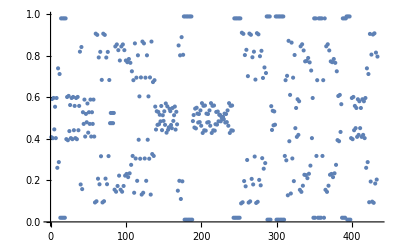
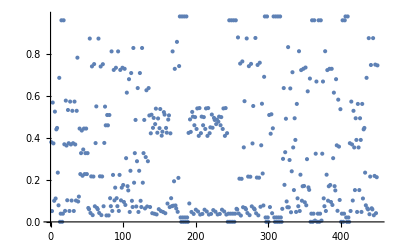
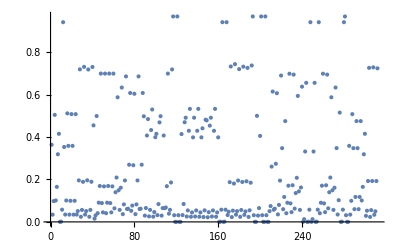
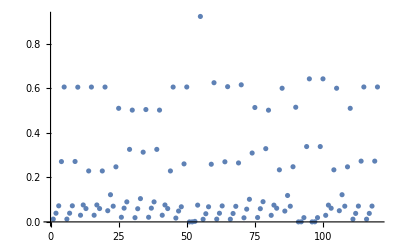
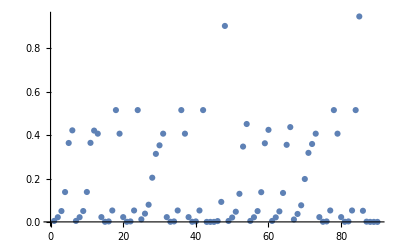
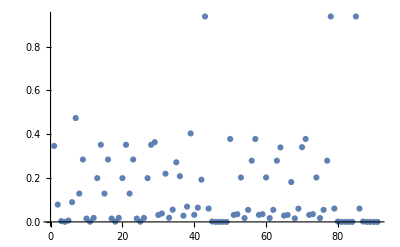

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
TableForm[emuSol[targets],TableHeadings->{targets,None}]
```

<acrn_c{(17)}> | 0.444655 | 0.227783 | 0.327562 |  |  |  | 
<acrn_m{(17)}> | 0.444655 | 0.227783 | 0.327562 |  |  |  | 
<ala-L_c{(123)}> | 0.454942 | 0.0153849 | 0.0307085 | 0.498965 |  |  | 
<arg-L_c{(123456)}> | 0.34671 | 0.0790057 | 0.0036681 | 0.000288849 | 0.00623032 | 0.0900714 | 0.474026
<asp-L_c{(1234)}> | 0.029972 | 0.075995 | 0.0598685 | 0.228723 | 0.605442 |  | 
<asp-L_m{(1234)}> | 0.0501822 | 0.122058 | 0.0705461 | 0.247233 | 0.509981 |  | 
<citr-L_c{(123456)}> | 0.129253 | 0.284703 | 0.0151837 | 0.00103862 | 0.0181832 | 0.199707 | 0.351931
<citr-L_m{(123456)}> | 0.129253 | 0.284703 | 0.0151837 | 0.00103862 | 0.0181832 | 0.199707 | 0.351931
<g3p_c{(123)}> | 0.413938 | 0.0320089 | 0.0844114 | 0.469642 |  |  | 
<glc-D_c{(123456)}> | 0.33991 | 0.0287035 | 0.0317499 | 0.181994 | 0.0161344 | 0.0604019 | 0.341106
<glc-D_r{(123456)}> | 0.378442 | 0.0319573 | 0.0353488 | 0.202608 | 0.017336 | 0.0549528 | 0.279355
<gln-L_c{(12345)}> | 3.2×10^-9 | 7.84×10^-7 | 0.000076832 | 0.00376477 | 0.0922368 | 0.903921 | 
<gln-L_m{(12345)}> | 0.00424019 | 0.0202166 | 0.0469889 | 0.129542 | 0.347478 | 0.451534 | 
<glu-L_c{(12345)}> | 0.00449265 | 0.0214203 | 0.0497821 | 0.137031 | 0.362675 | 0.424599 | 
<glu-L_m{(12345)}> | 0.00437397 | 0.0208545 | 0.0484691 | 0.13351 | 0.355531 | 0.437261 | 
<gly_c{(12)}> | 0.230526 | 0.0782817 | 0.691192 |  |  |  | 
<glyc3p_c{(123)}> | 0.499892 | 0.0297224 | 0.0650894 | 0.405297 |  |  | 
<mal-L_c{(1234)}> | 0.0295011 | 0.0752529 | 0.0614265 | 0.233747 | 0.600073 |  | 
<mal-L_m{(1234)}> | 0.0486258 | 0.11859 | 0.0703481 | 0.24765 | 0.514786 |  | 
<orn_c{(12345)}> | 0.406966 | 0.0220086 | 0.000519905 | 0.00215312 | 0.0526253 | 0.515727 | 
<orn_m{(12345)}> | 0.406966 | 0.0220086 | 0.000519905 | 0.00215312 | 0.0526253 | 0.515727 | 
<ser-L_c{(123)}> | 0.100979 | 0.165055 | 0.318741 | 0.415225 |  |  |

```mathematica
With[{e=SubstrateEMUs[emuEq⟦6⟧]},
TableForm[emuSol[e],TableHeadings->{e,None}]]
```

<arg-L_i{(123456)}> | 6.4×10^-11 | 1.8816×10^-8 | 2.30496×10^-6 | 0.000150591 | 0.00553421 | 0.10847 | 0.885842
<glc-D_i{(123456)}> | 6.4×10^-11 | 1.8816×10^-8 | 2.30496×10^-6 | 0.000150591 | 0.00553421 | 0.10847 | 0.885842
<glycogen_i{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12
<prot_arg_i{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12

```mathematica
With[{e=InternalEMUs[emuEq⟦6⟧]},
TableForm[emuSol[e],TableHeadings->{e,None}]]
```

<arg-L_c{(123456)}> | 0.34671 | 0.0790057 | 0.0036681 | 0.000288849 | 0.00623032 | 0.0900714 | 0.474026
<argsuc_c{(12358a)}> | 0.129253 | 0.284703 | 0.0151837 | 0.00103862 | 0.0181832 | 0.199707 | 0.351931
<citr-L_c{(123456)}> | 0.129253 | 0.284703 | 0.0151837 | 0.00103862 | 0.0181832 | 0.199707 | 0.351931
<citr-L_m{(123456)}> | 0.129253 | 0.284703 | 0.0151837 | 0.00103862 | 0.0181832 | 0.199707 | 0.351931
<f6p_c{(123456)}> | 0.363813 | 0.031641 | 0.0382907 | 0.219937 | 0.0186233 | 0.0558128 | 0.271882
<fdp_c{(123456)}> | 0.208691 | 0.0282871 | 0.0694869 | 0.403693 | 0.0322736 | 0.0649321 | 0.192637
<g1p_c{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12
<g6p_c{(123456)}> | 0.378442 | 0.0319573 | 0.0353488 | 0.202608 | 0.017336 | 0.0549528 | 0.279355
<g6p_r{(123456)}> | 0.378442 | 0.0319573 | 0.0353488 | 0.202608 | 0.017336 | 0.0549528 | 0.279355
<glc-D_c{(123456)}> | 0.33991 | 0.0287035 | 0.0317499 | 0.181994 | 0.0161344 | 0.0604019 | 0.341106
<glc-D_r{(123456)}> | 0.378442 | 0.0319573 | 0.0353488 | 0.202608 | 0.017336 | 0.0549528 | 0.279355
<glycogen_c{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12
<prot_arg_c{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12